```mathematica
Clear[x0]
```

```mathematica
x0[t,tau]=(c1[tau]*Cos[w*t]+c2[tau]*Sin[w*t]);
```

```mathematica
D[x0[t,tau],tau]
```

Cos[t w] c1'[tau]+Sin[t w] c2'[tau]

```mathematica
x0[t,tau]^3//TrigReduce
```

1/4 (3 c1[tau]^3 Cos[t w]+3 c1[tau] c2[tau]^2 Cos[t w]+c1[tau]^3 Cos[3 t w]-3 c1[tau] c2[tau]^2 Cos[3 t w]+3 c1[tau]^2 c2[tau] Sin[t w]+3 c2[tau]^3 Sin[t w]+3 c1[tau]^2 c2[tau] Sin[3 t w]-c2[tau]^3 Sin[3 t w])

```mathematica
rhs=-b*x0[t,tau]^3+Cos[t]-2*D[x0[t,tau],tau,t]-σ*x0[t,tau]/.w->1//TrigReduce
```

1/4 (4 Cos[t]-4 σ c1[tau] Cos[t]-3 b c1[tau]^3 Cos[t]-3 b c1[tau] c2[tau]^2 Cos[t]-b c1[tau]^3 Cos[3 t]+3 b c1[tau] c2[tau]^2 Cos[3 t]-4 σ c2[tau] Sin[t]-3 b c1[tau]^2 c2[tau] Sin[t]-3 b c2[tau]^3 Sin[t]-3 b c1[tau]^2 c2[tau] Sin[3 t]+b c2[tau]^3 Sin[3 t]+8 Sin[t] c1'[tau]-8 Cos[t] c2'[tau])

```mathematica
Coefficient[rhs/.w->1,Cos[t]]
```

1/4 (4-4 σ c1[tau]-3 b c1[tau]^3-3 b c1[tau] c2[tau]^2-8 c2'[tau])

```mathematica
Coefficient[rhs/.w->1,Sin[t]]
```

1/4 (-4 σ c2[tau]-3 b c1[tau]^2 c2[tau]-3 b c2[tau]^3+8 c1'[tau])

```mathematica
Solve[{4-4 σ c1[tau]-3 b c1[tau]^3-3 b c1[tau] c2[tau]^2==0,-4 σ c2[tau]-3 b c1[tau]^2 c2[tau]-3 b c2[tau]^3==0},{c1[tau],c2[tau]}]
```

{{c1[tau]→1/3 (-(2 2^(2/3) σ)/((9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))+(2^(1/3) (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))/b),c2[tau]→0},{c1[tau]→(2^(2/3) (1+ⅈ √3) σ)/(3 (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))-((1-ⅈ √3) (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))/(3 2^(2/3) b),c2[tau]→0},{c1[tau]→(2^(2/3) (1-ⅈ √3) σ)/(3 (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))-((1+ⅈ √3) (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))/(3 2^(2/3) b),c2[tau]→0}}

```mathematica
1/3 (-(2 2^(2/3) σ)/((9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))+(2^(1/3) (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))/b)//FullSimplify
```

(-2 2^(2/3) b σ+2^(1/3) (9 b^2+√(b^3 (81 b+16 σ^3)))^(2/3))/(3 b (9 b^2+√(b^3 (81 b+16 σ^3)))^(1/3))

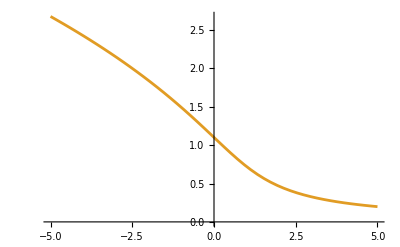

```mathematica
Plot[{(2^(2/3) (1-ⅈ √3) σ)/(3 (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))-((1+ⅈ √3) (9 b^2+√(81 b^4+16 b^3 σ^3))^(1/3))/(3 2^(2/3) b),(-2 2^(2/3) b σ+2^(1/3) (9 b^2+√(b^3 (81 b+16 σ^3)))^(2/3))/(3 b (9 b^2+√(b^3 (81 b+16 σ^3)))^(1/3))/.b->1},{σ,-5,5}]
```